# 2014 Belediye Seçim Analizi

### Verilerin yüklenmesi

Mathematica doğrudan Json yükleyebiliyor.

```mathematica
a=Import[FileNameJoin[{NotebookDirectory[],"..","ankara","ankara31mart2014.json"}]];
```

Her eleman bir "rule list".

```mathematica
a[[1]]
```

{akp_oy→160,alan→AKYURT IMAM HATIP LISESI,bbp_oy→2,btp_oy→5,chp_oy→16,date_value→31.03.2014,dp_oy→1,dsp_oy→0,dyp_oy→0,gecerli_oy→233,gecersiz_oy→23,hdp_oy→1,hep_oy→0,hkp_oy→1,hop_oy→0,il→ANKARA,ilce→AKYURT,itirazli_gecerli_oy→0,itirazsiz_gecerli_oy→233,kanun_geregi_oy_kullanan→0,kayitli_secmen→267,kullanilan_toplam_oy→256,ldp_oy→0,mhp_oy→37,mp_oy→0,oy_kullanan_kayitli_secmen→256,sandik→1003,sp_oy→8,time_value→22:25,turkp_oy→1,url→http://sts.chp.org.tr/SonucDetay.aspx?sid=205409,yp_oy→1}

Bunları vektöre çevirmek kolay:

```mathematica
akpOy="akp_oy"/.a;
chpOy="chp_oy"/.a;
mhpOy="mhp_oy"/.a;
ilce="ilce"/.a;
sandik="sandik"/.a;
itirazli="itirazli_gecerli_oy"/.a;
itierazsiz="itirazsiz"/.a;
kanun="kanun_geregi_oy_kullanan"/.a;
kayitli="kayitli_secmen"/.a;
toplam="kullanilan_toplam_oy"/.a;
```

Gelmişken oranları da bir hesaplayalım:

```mathematica
katilim=toplam/kayitli;
akpOran=akpOy/toplam;
chpOran=chpOy/toplam;
mhpOran=mhpOy/toplam;
```

İlk olarak sandık katılım oranının dağılımını çizdirelim:

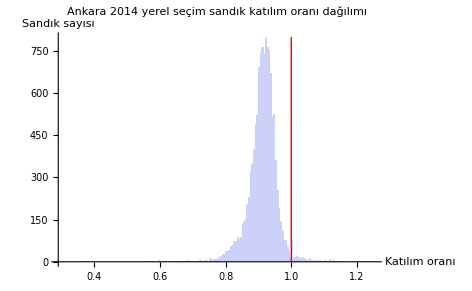

```mathematica
Histogram[
katilim,
PlotLabel->"Ankara 2014 yerel seçim sandık katılım oranı dağılımı",
AxesLabel->{"Katılım oranı","Sandık sayısı"},
Epilog->{
Red,
Line[{{1.0,0},{1.0,800}}]
}
]
```

Bundan sonra sözü edilen katılım oranına karşı AKP ve CHP oy oranlarını çizdirelim.

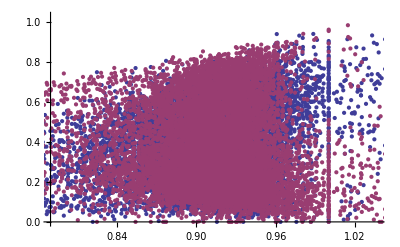

```mathematica
ListPlot[
{
{toplam/kayitli,akpOy/kayitli}ᵀ,
{toplam/kayitli,chpOy/kayitli}ᵀ
}
]
```